0.05

60

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

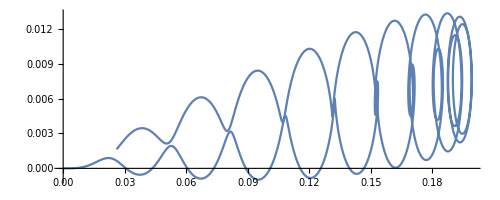

```mathematica
q=0.05
T=60
s=NDSolve[{x''[t]+2q (-x[t]Cos[2t]-y[t]Sin[2t])==0,y''[t]+2q (y[t]Cos[2t]-x[t]Sin[2t])==0,x[0]==y[0]==0,x'[0]==0.01,y'[0]==0},{x,y},{t,T}]
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,T},PlotPoints->600]
```